```mathematica
Quit[]
```

```mathematica
$LoadAddOns={"FeynArts","FeynHelpers"};
Needs["FeynCalc`"]
```

FeynCalc 10.2.1 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (27 Mar 2025) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 2.0.0 (). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynHelpers in your research, please evaluate FeynHelpersHowToCite[] to learn how to cite this work.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
CKM = IndexDelta;
Neglect[ME] = Neglect[ME2] = 0;
$FAVerbose=1;
(* use generic model from FeynCalc! The SUNF and SUNT functions in the .mod file have to be replaced by FASUNF and FASUNT *)
SetOptions[InsertFields, Model ->"../../FA_models/SMS-stop-SMQCD-NLO_FA",InsertionLevel-> {Particles}];
SetOptions[Paint, PaintLevel -> {Particles}];
SetOptions[CreateTopologies, ExcludeTopologies -> {TadpoleCTs,Tadpoles}];
```

## Top Vertex Correction

generic model {Lorentz} initialized

classes model {../../FA_models/SMS-stop-SMQCD-NLO_FA} initialized

in total: 6 Particles insertions

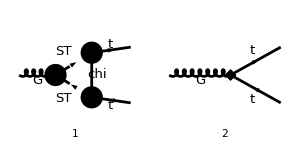

```mathematica
tops = CreateTopologies[1, 1->2,  ExcludeTopologies -> {TadpoleCTs,Tadpoles}];
topsCT = CreateCTTopologies[1,1->2];
processTT =  { V[1]} -> {F[3],-F[3]};
allDiags = InsertFields[Join[tops,topsCT],processTT, InsertionLevel-> {Particles},ExcludeParticles->{V[2],V[3],V[4],V[1]}];
goodDiags = DiagramExtract[allDiags,{1,4}];
Paint[goodDiags,ColumnsXRows->{2,1},ImageSize->{ 300,150},PaintLevel->{Particles},Numbering->Simple,AutoEdit->True];
```

```mathematica
ampA=FCFAConvert[CreateFeynAmp[goodDiags,PreFactor->1,Truncated->True]/.{SUNT->FASUNT, GS-> √(4 Pi aS)},IncomingMomenta->{p},OutgoingMomenta->{p1,p2},LoopMomenta->{q},LorentzIndexNames->{μ},List->False,DropSumOver->True,SMP->True,List->False,Contract->False,ChangeDimension->D,UndoChiralSplittings->True,FinalSubstitutions-> M$FACouplings]/.{FR$deltaZ[{G,G},{{}}]->deltaZG,FR$deltaZ[{t,t},{{}},"L"]->deltaZL,FR$deltaZ[{t,t},{{}},"R"]->deltaZR,FR$delta[{MT},{}]->deltaM,FR$delta[{aS},{}]->deltaaS,aS->gs^2/(4 Pi)}
```

in total: 2 Particles amplitudes

(√(gs^2) T_Col2Col3^Glu1 (p1+p2-2 q)^μ (-ⅈ yDM (γ̄)^7).(mChi+γ·(p1-q)).(-ⅈ yDM (γ̄)^6))/((q^2-mST^2).((q-p1)^2-mChi^2).((-p1-p2+q)^2-mST^2))-(2 ⅈ π γ^μ.(γ̄)^7 T_Col2Col3^Glu1 (deltaaS+(deltaZG gs^2)/(4 π)+(deltaZL gs^2)/(2 π)))/(√(gs^2))-(2 ⅈ π γ^μ.(γ̄)^6 T_Col2Col3^Glu1 (deltaaS+(deltaZG gs^2)/(4 π)+(deltaZR gs^2)/(2 π)))/(√(gs^2))

Since we know there are no deltaZG corrections of order yDM, we can set deltaZG=0, which also implies deltaaS =0

```mathematica
ampB =FullSimplify[SUNSimplify[DiracSimplify[ampA]]/.{deltaZG->0,deltaaS->0},Assumptions->{gs>0}]
```

gs T_Col2Col3^Glu1 (-(yDM^2 (p1^μ+p2^μ-2 q^μ) ((γ·p1).(γ̄)^6-(γ·q).(γ̄)^6))/((q^2-mST^2).((p1-q)^2-mChi^2).((p1+p2-q)^2-mST^2))-ⅈ deltaZL γ^μ.(γ̄)^7-ⅈ deltaZR γ^μ.(γ̄)^6)

```mathematica
FCClearScalarProducts[];
SPD[p1,p2]=1/2(s-SPD[p1,p1]-SPD[p2,p2]);
ampC = TID[ampB,q,UsePaVeBasis->True,PaVeAutoReduce->True,ToPaVe->True]//Simplify
```

-ⅈ gs T_Col2Col3^Glu1 (2 π^2 yDM^2 γ^μ.(γ̄)^6 C_00(s,p1^2,p2^2,mST^2,mST^2,mChi^2)+π^2 yDM^2 (p1^μ-p2^μ) (γ·p1).(γ̄)^6 C_1(s,p1^2,p2^2,mST^2,mST^2,mChi^2)-π^2 yDM^2 (p1^μ-p2^μ) (γ·p2).(γ̄)^6 C_1(s,p2^2,p1^2,mST^2,mST^2,mChi^2)+2 π^2 yDM^2 p1^μ (γ·p1).(γ̄)^6 C_11(s,p1^2,p2^2,mST^2,mST^2,mChi^2)+2 π^2 yDM^2 p2^μ (γ·p2).(γ̄)^6 C_11(s,p2^2,p1^2,mST^2,mST^2,mChi^2)-2 π^2 yDM^2 (p1^μ (γ·p2).(γ̄)^6+p2^μ (γ·p1).(γ̄)^6) C_12(p1^2,s,p2^2,mChi^2,mST^2,mST^2)+deltaZL γ^μ.(γ̄)^7+deltaZR γ^μ.(γ̄)^6)

## Check Divergencies

Divergences from loop integrals:

```mathematica
lInts = Cases2[ampC,PaVe];
lIntsUVsub = Table[lInt->PaXEvaluateUV[lInt],{lInt,lInts}];
```

Divergences from  counter-terms
From the self-energy renormalization we have:
deltaZL = π^2 MT^2 yDM^2 B1'(MT^2) and 
          deltaZR = π^2 yDM^2 (MT^2 B1'(MT^2)+B1(MT^2))
and since B1' has no UV divergences:

```mathematica
deltaZRUV= Pi^2 yDM^2 PaXEvaluateUV[B1[MT^2,mChi^2,mST^2]];
deltaZLUV= 0;
```

```mathematica
ampCUV=ampC/.lIntsUVsub/.{deltaZR->deltaZRUV,deltaZL->deltaZLUV}
```

0

## Renormalization Conditions

The renormalization condition requires the loop correction (plus counter-terms) to vanish at zero momentum (p=0=p1+p2)
Therefore it is convenient to first set p1=-p2

```mathematica
ampZero=Simplify[DiracSimplify[ampB/.{p1->-p2}]]
```

-ⅈ gs T_Col2Col3^Glu1 (-(2 ⅈ yDM^2 q^μ ((γ·p2).(γ̄)^6+(γ·q).(γ̄)^6))/((q^2-mST^2).((p2+q)^2-mChi^2).(q^2-mST^2))+deltaZL γ^μ.(γ̄)^7+deltaZR γ^μ.(γ̄)^6)

```mathematica
ampZeroC = TID[ampZero,q,UsePaVeBasis->True,PaVeAutoReduce->True,ToPaVe->True]/.{Pair[Momentum[p2,D],Momentum[p2,D]]->MT^2}//Simplify
```

-ⅈ gs T_Col2Col3^Glu1 (γ^μ.(γ̄)^6 (2 π^2 yDM^2 C_00(0,MT^2,MT^2,mST^2,mST^2,mChi^2)+deltaZR)+4 π^2 yDM^2 p2^μ (γ·p2).(γ̄)^6 (C_1(0,MT^2,MT^2,mST^2,mST^2,mChi^2)+C_11(0,MT^2,MT^2,mST^2,mST^2,mChi^2)+C_12(MT^2,0,MT^2,mChi^2,mST^2,mST^2))+deltaZL γ^μ.(γ̄)^7)

The renormalization condition is ubar(-p2).G.v(p2) = 0, hence DiracSlash[p2] terms can be simplified when applied over the spinors:

```mathematica
ampZeroD=Simplify[DiracSimplify[SpinorUBar[-p2,MT].ChangeDimension[ampZeroC,4].SpinorV[p2,MT]]]
```

-ⅈ gs T_Col2Col3^Glu1 ((2 π^2 yDM^2 C_00(0,MT^2,MT^2,mST^2,mST^2,mChi^2)+deltaZR) (φ(-OverBar[p2],MT)).(γ̄)^μ.(γ̄)^6.(φ(-OverBar[p2],MT))-4 π^2 MT yDM^2 OverBar[p2]^μ (φ(-OverBar[p2],MT)).(γ̄)^6.(φ(-OverBar[p2],MT)) (C_1(0,MT^2,MT^2,mST^2,mST^2,mChi^2)+C_11(0,MT^2,MT^2,mST^2,mST^2,mChi^2)+C_12(MT^2,0,MT^2,mChi^2,mST^2,mST^2))+deltaZL (φ(-OverBar[p2],MT)).(γ̄)^μ.(γ̄)^7.(φ(-OverBar[p2],MT)))

Finally, the p2^μ term can be rewritten using the Gordon Identity:

```mathematica
Print[SpinorUBar[-p2,MT].GA[μ,6].SpinorV[p2,MT]," = ",GordonSimplify[ SpinorUBar[-p2,MT].GA[μ,6].SpinorV[p2,MT]]]
```

ū(-p2,MT).(γ̄)^μ.(γ̄)^6.v(p2,MT) = -(φ(-OverBar[p2],MT)).(γ̄)^μ.(γ̄)^7.(φ(-OverBar[p2],MT))-(2 (φ(-OverBar[p2],MT)).(γ̄)^6.(φ(-OverBar[p2],MT)) OverBar[p2]^μ)/MT

```mathematica
ampZeroE=Simplify[ampZeroD/.{Spinor[-Momentum[p2],MT,1].DiracGamma[6].Spinor[-Momentum[p2],MT,1]*Pair[LorentzIndex[μ],Momentum[p2]]->-MT/2(Spinor[-Momentum[p2],MT,1].DiracGamma[LorentzIndex[μ]].Spinor[-Momentum[p2],MT,1])}];
```

```mathematica
ampZeroF=FullSimplify[DiracSimplify[ampZeroE,DiracSubstitute67->True]]
```

-1/2 ⅈ gs T_Col2Col3^Glu1 ((φ(-OverBar[p2],MT)).(γ̄)^μ.(φ(-OverBar[p2],MT)) (2 π^2 yDM^2 (C_00(0,MT^2,MT^2,mST^2,mST^2,mChi^2)+2 MT^2 (C_1(0,MT^2,MT^2,mST^2,mST^2,mChi^2)+C_11(0,MT^2,MT^2,mST^2,mST^2,mChi^2)+C_12(MT^2,0,MT^2,mChi^2,mST^2,mST^2)))+deltaZL+deltaZR)+(φ(-OverBar[p2],MT)).(γ̄)^μ.(γ̄)^5.(φ(-OverBar[p2],MT)) (2 π^2 yDM^2 C_00(0,MT^2,MT^2,mST^2,mST^2,mChi^2)-deltaZL+deltaZR))

The vector and axial coefficients should both vanish:

```mathematica
fV=Coefficient[ampZeroF,Spinor[-Momentum[p2],MT,1].DiracGamma[LorentzIndex[μ]].Spinor[-Momentum[p2],MT,1]]/(-I √aS √Pi SUNTF[{SUNIndex[Glu1]},SUNFIndex[Col2],SUNFIndex[Col3]])
fA=Coefficient[ampZeroF,Spinor[-Momentum[p2],MT,1].DiracGamma[LorentzIndex[μ]].DiracGamma[5].Spinor[-Momentum[p2],MT,1]]/(-I √aS √Pi SUNTF[{SUNIndex[Glu1]},SUNFIndex[Col2],SUNFIndex[Col3]])
```

(gs (2 π^2 yDM^2 (C_00(0,MT^2,MT^2,mST^2,mST^2,mChi^2)+2 MT^2 (C_1(0,MT^2,MT^2,mST^2,mST^2,mChi^2)+C_11(0,MT^2,MT^2,mST^2,mST^2,mChi^2)+C_12(MT^2,0,MT^2,mChi^2,mST^2,mST^2)))+deltaZL+deltaZR))/(2 √π √aS)

(gs (2 π^2 yDM^2 C_00(0,MT^2,MT^2,mST^2,mST^2,mChi^2)-deltaZL+deltaZR))/(2 √π √aS)

```mathematica
$Assumptions={mChi>0,mST>0,MT>0,MT<mChi+mST};
deltaZLexpr= Pi^2 MT^2 yDM^2 D[PaXEvaluate[B1[psq,mChi^2,mST^2],PaXImplicitPrefactor->1/(2 Pi)^(4- 2 Epsilon)],psq]/.{psq->MT^2};
deltaZRexpr=Pi^2 yDM^2 PaXEvaluate[B1[MT^2,mChi^2,mST^2],PaXImplicitPrefactor->1/(2 Pi)^(4- 2 Epsilon)];
```

```mathematica
lIntsExpr=Table[lInt->PaXEvaluate[lInt,PaXImplicitPrefactor->1/(2 Pi)^(4- 2 Epsilon)],{lInt,Cases2[ampZeroC,PaVe]}];
```

```mathematica
fVexpr=FullSimplify[fV/.lIntsExpr/.{deltaZL->deltaZLexpr,deltaZR->deltaZRexpr},Assumptions->{mST>MT+mChi,mChi>0,mST>0,MT>0,MT<mChi+mST}];
```

(gs yDM^2 (MT^4 √((mChi-mST-MT) (mChi+mST-MT) (mChi-mST+MT) (mChi+mST+MT)) log((4 π μ^2 mChi^2)/mST^2)-mChi^2 MT^2 √((mChi-mST-MT) (mChi+mST-MT) (mChi-mST+MT) (mChi+mST+MT)) log(μ^2/mST^2)-MT^2 √((mChi-mST-MT) (mChi+mST-MT) (mChi-mST+MT) (mChi+mST+MT)) (2 mChi^2-2 mST^2+MT^2)+2 (mChi-mST) (mChi+mST) √((mChi-mST-MT) (mChi+mST-MT) (mChi-mST+MT) (mChi+mST+MT)) (mChi^2-mST^2+MT^2) log(mChi/mST)+mChi^2 MT^2 log(μ^2/mChi^2) √((mChi-mST-MT) (mChi+mST-MT) (mChi-mST+MT) (mChi+mST+MT))+2 ((mChi^2-mST^2)^3-MT^2 (mChi^4+mChi^2 mST^2-2 mST^4)-mST^2 MT^4) log((2 mChi mST)/(mChi^2+√((mChi-mST-MT) (mChi+mST-MT) (mChi-mST+MT) (mChi+mST+MT))+mST^2-MT^2))-MT^4 √((mChi-mST-MT) (mChi+mST-MT) (mChi-mST+MT) (mChi+mST+MT)) log((4 π μ^2)/mST^2)-2 MT^4 log(mChi) √((mChi-mST-MT) (mChi+mST-MT) (mChi-mST+MT) (mChi+mST+MT))))/(64 π^(5/2) MT^4 √(aS (mChi-mST-MT) (mChi+mST-MT) (mChi-mST+MT) (mChi+mST+MT)))

```mathematica
fAexpr=FullSimplify[fA/.lIntsExpr/.{deltaZL->deltaZLexpr,deltaZR->deltaZRexpr},Assumptions->{mST>MT+mChi,mChi>0,mST>0,MT>0,MT<mChi+mST}];
```

(gs yDM^2 (MT^4 √((mChi-mST-MT) (mChi+mST-MT) (mChi-mST+MT) (mChi+mST+MT)) log((4 π μ^2 mChi^2)/mST^2)-mChi^2 MT^2 √((mChi-mST-MT) (mChi+mST-MT) (mChi-mST+MT) (mChi+mST+MT)) log(μ^2/mST^2)-MT^2 √((mChi-mST-MT) (mChi+mST-MT) (mChi-mST+MT) (mChi+mST+MT)) (2 mChi^2-2 mST^2+MT^2)+2 (mChi-mST) (mChi+mST) √((mChi-mST-MT) (mChi+mST-MT) (mChi-mST+MT) (mChi+mST+MT)) (mChi^2-mST^2+MT^2) log(mChi/mST)+mChi^2 MT^2 log(μ^2/mChi^2) √((mChi-mST-MT) (mChi+mST-MT) (mChi-mST+MT) (mChi+mST+MT))+2 ((mChi^2-mST^2)^3-MT^2 (mChi^4+mChi^2 mST^2-2 mST^4)-mST^2 MT^4) log((2 mChi mST)/(mChi^2+√((mChi-mST-MT) (mChi+mST-MT) (mChi-mST+MT) (mChi+mST+MT))+mST^2-MT^2))-MT^4 √((mChi-mST-MT) (mChi+mST-MT) (mChi-mST+MT) (mChi+mST+MT)) log((4 π μ^2)/mST^2)-2 MT^4 log(mChi) √((mChi-mST-MT) (mChi+mST-MT) (mChi-mST+MT) (mChi+mST+MT))))/(64 π^(5/2) MT^4 √(aS (mChi-mST-MT) (mChi+mST-MT) (mChi-mST+MT) (mChi+mST+MT)))

## Check against analytical results

```mathematica
b1=Simplify[PaXEvaluate[B1[MT^2,mChi^2,mST^2],PaXImplicitPrefactor->1/(2 Pi)^(4-2 Epsilon)]/.{1/Epsilon->EulerGamma-Log[4 Pi],ScaleMu->mST}];
db1=Simplify[D[b1/.{MT-> √psq},psq]/.{psq->MT^2}];
solutionCTs={deltaM->-1/2 π^2 MT yDM^2 B1[MT^2],deltaZL->π^2 MT^2 yDM^2 Derivative[1][B1][MT^2],deltaZR->π^2 yDM^2 (MT^2 Derivative[1][B1][MT^2]+B1[MT^2])};
deltaCTRsol=1/(I Pi^2 yDM^2)(I deltaZR)/.solutionCTs/.{B1[MT^2]->Re[b1],Derivative[1][B1][MT^2]->Re[db1]};
deltaCTLsol=1/(I Pi^2 yDM^2)(I deltaZL)/.solutionCTs/.{B1[MT^2]->Re[b1],Derivative[1][B1][MT^2]->Re[db1]};
```

```mathematica
lA=1+xC^2+xT^2-2*xC-2*xT-2*xT*xC;
xC = mChi^2/mST^2;
xT=MT^2/mST^2;
lB=-lA;
deltaCTL1=(1/(128*xT^2*Sqrt[lA]*Pi^4))*((2*Sqrt[lA]*(xT*(-2+2 xC+xT)+(-(-1+xC)^2+xT)*Log[xC])-4*(-(-1+xC)^3+(-2+xC+xC^2) xT+xT^2)*Log[(1+xC+Sqrt[lA]-xT)/(2*Sqrt[xC])]));
deltaCTR1=(1/(128*xT^2*Sqrt[lA]*Pi^4))*((-1+xC-xT)*(Sqrt[lA]*(2*xT-(-1+xC+xT)*Log[xC])+2*((-2+xC)*xC+(-1+xT)^2)*Log[(1+xC+Sqrt[lA]-xT)/(2*Sqrt[xC])]));
deltaCTL2=(1/(128*xT^2*Pi^4))*(2*(xT*(-2+2*xC+xT)+(1/Sqrt[lB])(lB*(-1+xC)-(-1+xC)^3+2*(-1+xC)*xT+(1+xC) xT^2)*(-ArcTan[Sqrt[lB]/(1+xC-xT)])+(-(-1+xC)^2+xT)*Log[xC]));
deltaCTR2=(1/(128*xT^2*Pi^4))*(((2*(-(-1+xC)^3-(2+lB-2*xC)*xT+(1+xC)*xT^2)*(-ArcTan[Sqrt[lB]/(1+xC-xT)]))/Sqrt[lB]+(1-xC+xT)*(-2*xT+(-1+xC+xT)*Log[xC])));
```

```mathematica
Simplify[deltaCTLsol-2 deltaCTL1,Assumptions->{mST>MT+mChi,mChi>0,mST>0,MT>0,MT<mChi+mST}]
Simplify[deltaCTRsol-2 deltaCTR1,Assumptions->{mST>MT+mChi,mChi>0,mST>0,MT>0,MT<mChi+mST}]
```

0

0

The region with an imaginary part needs to be checked numerically:

```mathematica
deltaCTLsol/.{mST->800.,mChi->700,MT->173.}
2 deltaCTL2/.{mST->800.,mChi->700,MT->173.}
deltaCTRsol/.{mST->800.,mChi->700,MT->173.}
2 deltaCTR2/.{mST->800.,mChi->700,MT->173.}
```

-2.79603×10^-6

-2.79603×10^-6

-0.0000322656

-0.0000322656